## Function to Solve Schrödinger’s Equation

```mathematica
showStatus[status_]:=LinkWrite[$ParentLink,SetNotebookStatusLine[FrontEnd`EvaluationNotebook[],ToString[status]]]
findEvolutionOperator[Hin_, Tmax_?NumericQ, acc_:10]:=(
funcs=Array[ψ[#2 + Length[Hin]*(#1- 1)][t]&,{Length[Hin],Length[Hin]}];
equations=Flatten@Join[Thread[Hin.funcs == ⅈ*D[funcs,t]],Thread[funcs==IdentityMatrix[Length[Hin]]/.t->0]];
NDSolveValue[equations,funcs,{t,0,Tmax}, AccuracyGoal->acc, PrecisionGoal->acc, EvaluationMonitor:>showStatus["t = "<>ToString[CForm[t]]], MaxSteps->10^6]
)
```

## Driving with 1/2 the Transition Frequency

This is a toy model of the nuclear spin qubit in the {|g↓⇓⟩, |e↓⇓⟩} subspace.  It’s just the Rabi model with an extra σ_z driving term.  When the frequency equals the transition energy (ω = Δ) there are rapid oscillations which quickly subside as the frequency is changed.  Weirdly, though, there are strong oscillations when ω = Δ/2.

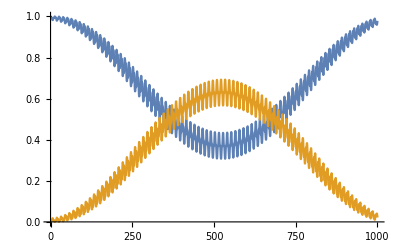

```mathematica
Ω = .05;
Δ = 1;
ω = Δ/2;
Tmax = 1000;
H = {{-Ω*Cos[ω*t], Ω*Cos[ω*t]}, {Ω*Cos[ω*t], Δ + Ω*Cos[ω*t]}};
U = findEvolutionOperator[H, Tmax];

Plot[{Abs[U[[1, 1]]]^2, Abs[U[[2, 1]]]^2}, {t, 0, Tmax}]
```

These oscillations can actually be made into complete transitions by shifting the frequency slightly.  I’m not sure how to derive that shift yet, but I can approximate it with Floquet theory.

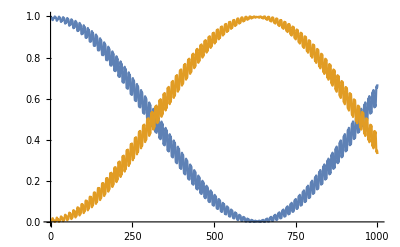

```mathematica
Ω = .05;
Δ = 1;
ω = Δ/2 + .0018;
Tmax = 1000;
H = {{-Ω*Cos[ω*t], Ω*Cos[ω*t]}, {Ω*Cos[ω*t], Δ + Ω*Cos[ω*t]}};
U = findEvolutionOperator[H, Tmax];

Plot[{Abs[U[[1, 1]]]^2, Abs[U[[2, 1]]]^2}, {t, 0, Tmax}]
```

## Driving with 1/3 Transition Frequency

The weirder thing is that the plain Rabi model can be driven with a frequency near Δ/3.  I think this should work with any odd integer, but it’d keep getting slower.  I found the frequency shift with optimization.

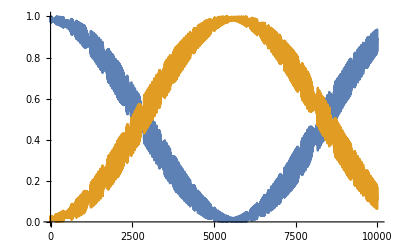

```mathematica
Ω = .1;
Δ = 1;
ω = Δ/3 + 0.0037592;
Tmax = 10000;
H = {{0, Ω*Cos[ω*t]}, {Ω*Cos[ω*t], Δ}};
U = findEvolutionOperator[H, Tmax];

Plot[{Abs[U[[1, 1]]]^2, Abs[U[[2, 1]]]^2}, {t, 0, Tmax}]
```